```mathematica
383685+(383685*0.05*15)
```

671449.

```mathematica
383685*1.05^15
```

797654.

```mathematica
2/1.015
```

1.97044

```mathematica
1/0.015
```

66.6667

```mathematica
1500*0.015*66.6667
```

1500.

```mathematica
3.5/3
```

1.16667

```mathematica
12*1.06667
```

12.8

```mathematica
383685/13.8
```

27803.3

```mathematica
383685/12.8
```

29975.4

```mathematica
29775.4*12*1.06667
```

381126.

```mathematica
12/0.6667
```

17.9991

```mathematica
N[2/3]
```

0.666667

```mathematica
12/(2/3)
```

18

```mathematica
N[383685/19]
```

20193.9

```mathematica
12*(0.2/3)
```

0.8

```mathematica
383685/1.8
```

213158.

```mathematica
4*0.035
```

0.14

```mathematica
383685/1.14
```

336566.

```mathematica
0.035*4
```

0.14

```mathematica
336566+(0.035*336566*4)
```

383685.

```mathematica
Clear[fq2]
```

```mathematica
fq2[x_,m_,i_]:=x/(x+(x*i*m))
```

```mathematica
?fq2
```

Global`fq2

fq2[x_,m_,i_]:=x/(x+x i m)

```mathematica
fq2[x,m,0.015]==0.5
```

x/(x+0.015 m x)==0.5

```mathematica
Solve[fq2[x,m,0.015]==0.5]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{m→66.6667}}

```mathematica
1/0.05
```

20.

```mathematica
1/(3/4.5)
```

1.5

```mathematica
1/1.5
```

0.666667

```mathematica
100/1.5
```

66.6667

```mathematica
1/0.015
```

66.6667

```mathematica
fq2[x,(1/0.015),0.015]==0.5
```

True

3)

```mathematica
Clear[fq3]
fq3[x_]:=0.4*x+((x*0.2)*1.06^4)+((x*0.2)*1.06^4)*1.5
```

```mathematica
?fq3
```

Global`fq3

fq3[x_]:=0.4 x+(x 0.2) 1.06^4+((x 0.2) 1.06^4) 1.5

```mathematica
fq3[383685]
```

395671.

```mathematica
(3.5/3)/100
```

0.0116667

```mathematica
((3.5/3/100))*12
```

0.14

```mathematica
383685/1.14
```

336566.

4) Errada.

Questão 4: Uma dívida pode ser paga à vista com o valor igual ao numero do código de ID de sua matrícula, ou pode ser paga da seguinte forma: uma entrada de 40% e mais duas prestações mensais. A primeira vencendo daqui a 4 meses, a segunda parcela deve ser 50% maior que a primeira. Sabendo que a taxa de juro composto para o período deve ser mantida em 6% a.m., determine o valor das duas parcelas. Escreva os cálculos que justifique sua resposta ( DOIS PONTOS)

Correção.
-Graphics-

“na questão nuero 4 , voce precisa utilzar  o modelo de equivalencia de capitatis, e igualar   a  divida a duas parcelas  conforme solicita o enunciado.”

```mathematica
Solve[383685==383685*0.4+R/1.06^4+(R/1.06^4)*1.5,R]
```

{{R→116254.}}

Conferindo.

```mathematica
383685*0.4+116254/1.06^4+(116254/1.06^4)*1.5
```

383684.

```mathematica
383685*0.4
```

153474.

```mathematica
1.06^4
```

1.26248

```mathematica
1.06^4*2
```

2.52495

```mathematica
(383685-153474)*2.52495
```

581271.

```mathematica
N[581271/5]
```

116254.

P. 128: “Equivalência de capitais... pagamentos ou recebimentos em datas de vencimento distintas em pagamentos ou recebimentos “equivalentes” “porém numa mesma data” (...) maneira de transformar pagamentos (recebimentos) com datas de vencimento distintas em pagamentos (recebimentos) “equivalentes” — avaliados numa data “comum”.”

Equivalência de capitais é “traduzir” uma parcela n períodos à frente ou atrás a partir do momento onde seu valor é sabido, sabendo os juros. Basicamente,
R/(1+i)^n=x, sabido x, quanto maior a diferença de n (de x para o novo valor a se saber), maior a divisão e portanto mais perto de R, a parcela original, em que n=0, o valor.

```mathematica
Clear[fparcel]
fparcel[R_,i_,n_]:=R/(1+i)^n
```

Uma parcela no seu instante zero.

```mathematica
fparcel[20000,0.05,0]
```

20000.

Dado um valor no futuro, quanto seria a parcela agora?

```mathematica
Solve[fparcel[R,0.05,-6]==20000,{R}]
```

{{R→14924.3}}

p. 128 1)

```mathematica
p128e1=Solve[fparcel[15000,0.045,6]==x,x]
```

{{x→11518.4}}

```mathematica
fparcel[11518.4,0.045,-2]
```

12578.4

Correto. Então é obter o valor zero, depois reaplicar um novo prazo.

Lembre-se: n vai sempre no sentido inverso na equivalência de capitais (por estar no denominador).

p. 130 1)

Três valores de parcelas no futuro. Temos de cobrir este total no presente, dado a proporção dos juros. Descobrir ao mesmo juros qual valor zero equivale à soma.

```mathematica
{fparcel[220000,0.024,3],fparcel[120000,0.024,14],fparcel[140000,0.024,24]}
```

{204891.,86095.8,79237.2}

O que acontece é que estes valores não advêm da mesma dívida; são dívidas distintas que queremos agrupar em uma só. Por isso “x não deve ser igual nas três”.

```mathematica
Total[{fparcel[220000,0.024,3],fparcel[120000,0.024,14],fparcel[140000,0.024,24]}]
```

370224.

```mathematica
(*fparcel[370224,0.024,*)
```

Já é a resposta! Não entendi...

p. 132 2)

```mathematica
5000/1.025^0+2500/1.025^1+2500/1.025^2+2500/1.025^3+2500/1.025^4
```

14404.9

Entrada é o “pagamento” n. 1, de expoente 0, valor ainda sem o juros aplicado. O juros começa a ser aplicado depois do tempo zero, ou primeiro período, seja este segundo pagamento no antecipado, ou primeiro pagamento no postecipado. A parcela no ato é (1+i)^0 e a primeira parcela com juros é (1+i)^(1+).
“Entrada” é o primeiro pagamento no ato e isto é antecipado. Sem entrada é postecipado pois o primeiro pagamento é em 1 mês.

(Voltando do final.)

```mathematica
?fsuppa
```

Global`fsuppa

fsuppa[R_,i_,n_,R2_,nns_]:=R fani[i,n]+Total[Table[fvx[R2,i,nn],{nn,nns}]]

```mathematica
Table[fvx[R2,i,nn],{nn,nns}]
```

{0.914542 R2,0.836387 R2,0.764912 R2}

x+1.5x=60⇒x=60/2.5=24

```mathematica
60/2.5
```

24.

```mathematica
Clear[fp161]
fp161[R_,i_,n_]:=R*fani[i,n]+fvx[383685*0.24,i,4]+fvx[383685*0.36,i,5]
?fp161
```

Global`fp161

fp161[R_,i_,n_]:=R fani[i,n]+fvx[383685 0.24,i,4]+fvx[383685 0.36,i,5]

```mathematica
fp161[383685,0.06,2]
```

879601.

```mathematica
383685*fani[0.06,2]
```

703445.

O fani está estranho.

O valor é só das parcelas.

```mathematica
{fvx[383685*0.24,0.06,4],fvx[383685*0.36,0.06,5]}
```

{72939.5,103216.}

```mathematica
?fvx
```

Global`fvx

fvx[R_,i_,n_]:=R/(1+i)^n

```mathematica
(383685*0.24)/1.06^4
```

72939.5

```mathematica
(383685*0.36)/1.06^5
```

103216.

Unisul p. 160. MontanteValor atual da sequência uniforme com parcelas adicionais. V=R·a_(n¬i)+∑V_x. p. 153. Montante da sequência uniforme sem parcelas adicionais. M=R·S_(n¬i). O fator (1+i)^n/ié chamado fator de acumulação de capitais e representado por S_(n¬i) (S, n, cantoneira i). Mas isso não é a_(n¬i), que é ((1+i)^n-1)/((1+i)^n·i). O valor atual de uma sequência uniforme de termos postecipados é V=R·a_(n¬i). O valor atual de uma sequência uniforme de termos antecipados é V=R+R·a_(n-1¬i). ... Entender exatamente o que é a_(n+x¬i). Valor atual de sequência uniforme diferida é V_m=R·a_(n¬i)⇒V=(R·a_(n¬i))/(1+i)^m. m é o período de carência. Decompor e recompor essas funções e resolver.

```mathematica
ffatorac[i_,n_]:=(1+i)^n/i
```

```mathematica
Table[ffatorac[0.05,m],{m,1,12}]
```

{21.,22.05,23.1525,24.3101,25.5256,26.8019,28.142,29.5491,31.0266,32.5779,34.2068,35.9171}

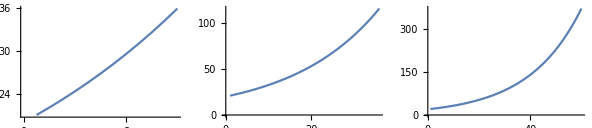

```mathematica
GraphicsRow[Table[ListPlot[Table[ffatorac[0.05,m],{m,1,mf}],ImageSize->Small,Joined->True],{mf,12,12+(24*2),24}]]
```

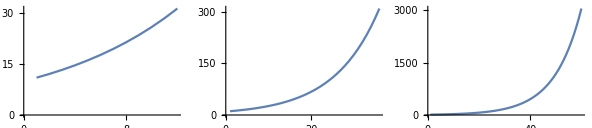

```mathematica
GraphicsRow[Table[ListPlot[Table[ffatorac[0.1,m],{m,1,mf}],ImageSize->Small,Joined->True],{mf,12,12+(24*2),24}]]
```

Fator de acumulação de capital cresce cada vez mais rápido quanto maior o juros.

É a razão entre os juros “acumulados” e o original, que tende a se tornar cada vez maior conforme o tempo, e mais rápido quanto maior o juros.
Ok, agora porquê S, n, cantoneira i? n e i são tempo e juros, respectivamente. n¬i implicaria dado certo tempo, com certo exponencial. Parece que a_(n¬i)=S_(n¬i). Portanto isso é o que tem na p. 153 sobre montante de uma sequência uniforme. M=R[a_(n¬i)]=R[((i+1)^n-1)/i]. Que é a multiplicação da parcela (R) pelo fator de acumulação de capitais.
Agora o com parcelas adicionais é só esta sequência uniforme com +ΣV_x, em que V_x é o valor atual de cada parcela adicional. E cada uma é R/(i+1)^n, em que n começa em zero, ou seja, um para um mês adicional. No exemplo ele primeiro calcula a_(n¬i), depois ΣV_x, que é: Σ R/(i+1)^n.

#### Resumo

Montante de sequência uniforme postecipada.
M=R·S_(n¬i)=R·(1+i)^n/i, com n entrada = 0 e n segunda parcela = 1.
Valor atual de sequência uniforme postecipada.
V=R·a_(n¬i)=R·((1+i)^n-1)/((1+i)^n·i), idem.
Valor atual de sequência uniforme postecipada com parcelas adicionais. (suppa)
V=R·a_(n¬i)+∑V_x=R·((1+i)^n-1)/((1+i)^n·i)+∑R/(1+i)^n (Não é realmente uma somatória.) (Parcelas adicionais “deflacionar” a parcela adicional ao momento do início dos juros.)
Valor atual de sequência uniforme antecipada.
V=R+R·a_(n-1¬i)=R+R·((1+i)^(n-1)-1)/((1+i)^(n-1)·i)(a_(n-1) significa apenas passar n-1 como n.) (O R inicial a mais com relação à postecipada é a primeira parcela imediata.)
Valor atual de sequência uniforme diferida.
V_m=R·a_(n¬i)⇒V=(R·a_(n¬i))/(1+i)^m(m = período de carência)

```mathematica
fani[i_,n_]:=((1+i)^n-1)/((1+i)^n*i)
```

```mathematica
fani[i,n-1]
```

((1+i)^(1-n) (-1+(1+i)^(-1+n)))/i

```mathematica
fvaloratualpostecipada2[R_,i_,n_]:=R*fani[i,n]
```

```mathematica
fvaloratualantecipada3[R_,i_,n_]:=R+R*fani[i,n-1]
```

```mathematica
fani[i,n]
```

((1+i)^-n (-1+(1+i)^n))/i

```mathematica
fani[i,n-1]
```

((1+i)^(1-n) (-1+(1+i)^(-1+n)))/i

```mathematica
fvx[R_,i_,n_]:=R/(1+i)^n
```

Exercício p. 161.

```mathematica
Table[fvx[3500,0.015,n],{n,6*0,6*3,6}]
```

{3500.,3200.9,2927.36,2677.19}

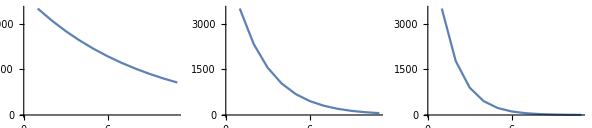

```mathematica
GraphicsRow[Table[ListPlot[Table[fvx[3500,i,n],{n,6*0,6*10,6}],ImageSize->Small,Joined->True],{i,0.02,0.12,0.05}]]
```

Parcelas adicionais aparentemente vão a zero com o tempo, tanto mais rápido quanto maior os juros.

```mathematica
fani[0.015,24]
```

20.0304

Correto até aqui.

```mathematica
Clear[fsuppa]
fsuppa[R_,i_,n_,R2_,nns_]:=R*fani[i,n]+Total[Table[fvx[R2,i,nn],{nn,nns}]]
?fsuppa
```

Global`fsuppa

fsuppa[R_,i_,n_,R2_,nns_]:=R fani[i,n]+Total[Table[fvx[R2,i,nn],{nn,nns}]]

```mathematica
?fvx
```

Global`fvx

fvx[R_,i_,n_]:=R/(1+i)^n

```mathematica
(*Not working*)
HoldForm[fvx[7000,0.015,6]]
```

fvx[7000,0.015,6]

```mathematica
nns={6,12,18}
Table[fvx[7000,0.015,n],{n,nns}]
Total[Table[fvx[7000,0.015,n],{n,nns}]]
```

{6,12,18}

{6401.8,5854.71,5354.38}

17610.9

```mathematica
N[fsuppa[3500,0.015,24,7000,{6,12,18}]]
```

87717.3

Resposta é 87717,31.

Anteriores:

```mathematica
0.4*383685+(383685*0.06^4)+2*(383685*0.06^4)
```

153489.

```mathematica
0.4*383685+((383685*0.06^4)*0.2)+(2*(383685*0.06^4)*0.2)
```

153477.

```mathematica
0.4*383685+(383685*0.06^4)+(383685*0.2)+2*((383685*0.06^4)+(383685*0.2))
```

383700.

```mathematica
3*1.06
```

3.18

```mathematica
3*1.06^4
```

3.78743

```mathematica
383685*0.2*1.06^4
```

96878.7

```mathematica
96878.7*1.5
```

145318.

```mathematica
(383685*0.4)+(383685*0.2*1.06^4)+(96878.7*1.5)
```

395671.

```mathematica
N[4/3]
```

1.33333

```mathematica
N[4/3]*0.01
```

0.0133333

```mathematica
(1+N[4/3]*0.01)^1
```

1.01333

```mathematica
Clear[fq4]
```

```mathematica
fq4[x_]:=(40x)/100+(20x)/100*(1+0.06)^4+1.5*((20x)/100*(1+0.06)^4)
```

```mathematica
?fq4
```

Global`fq4

fq4[x_]:=(40 x)/100+1/100 (20 x) (1+0.06)^4+1/100 1.5 ((20 x) (1+0.06)^4)

```mathematica
fq4[383685]
```

395671.

```mathematica
fq4a[x_]:=(20x)/100*(1+0.06)^4
```

```mathematica
Clear[fq4b]
fq4b[x_]:=(40x)/100+fq4a[x]+1.5*fq4a[x]
```

```mathematica
fq4b[383685]
```

395671.

```mathematica
fq4a[383685]
```

96878.7

```mathematica
1.5*fq4a[383685]
```

145318.

Fórmulas.

```mathematica
∑_(n=1)^4 n
```

10

```mathematica
Clear[su]
su[R_,i_,n_]:=∑_(x=1)^n R/(1+i)^x
```

```mathematica
?su
```

Global`su

su[R_,i_,n_]:=∑_(x=1)^n R/(1+i)^x

```mathematica
Table[su[1000,0.05,a],{a,1,12}]
```

{952.381,1859.41,2723.25,3545.95,4329.48,5075.69,5786.37,6463.21,7107.82,7721.73,8306.41,8863.25}

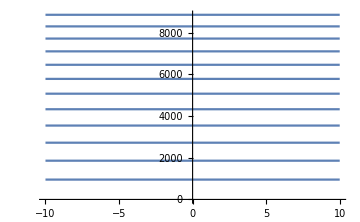

```mathematica
Plot[Table[su[1000,0.05,a],{a,1,12}],{x,-10,10},ImageSize->Medium]
```

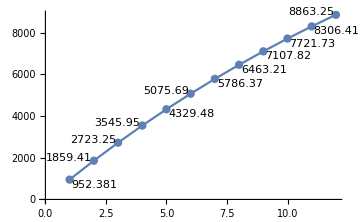

```mathematica
ListPlot[Labeled[#,#]&/@Table[su[1000,0.05,a],{a,1,12}],Joined->True,Mesh->All,ImageSize->Medium]
```

```mathematica
Clear[suplot]
suplot[suf_]:=Plot[Table[suf[1000,0.05,a],{a,1,12}],{x,-10,10},ImageSize->Small]
```

```mathematica
?suplot
```

Global`suplot

suplot[suf_]:=Plot[Table[suf[1000,0.05,a],{a,1,12}],{x,-10,10},ImageSize→Small]

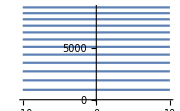

```mathematica
suplot[Function[{R,i,n},∑_(x=1)^n R/(1+i)^x]]
```

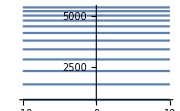

```mathematica
suplot[Function[{R,i,n},∑_(x=1)^n R/(1.1+i)^x]]
```

```mathematica
suplot[Function[{R,i,n},∑_(x=1)^n R/(1+i)^x]]
```

-Graphics-

```mathematica
Function[{R,i,n},∑_(x=1)^n R/(1+i)^x][R,i,3] // TraditionalForm
```

R/(i+1)+R/(i+1)^2+R/(i+1)^3

```mathematica
Table[Function[{R,i,n},∑_(x=1)^n R/(1+i)^x][1000,0.05,n],{n,1,20}]
```

{952.381,1859.41,2723.25,3545.95,4329.48,5075.69,5786.37,6463.21,7107.82,7721.73,8306.41,8863.25,9393.57,9898.64,10379.7,10837.8,11274.1,11689.6,12085.3,12462.2}

```mathematica
1.05^4
```

1.21551

```mathematica
1.05^4-1
```

0.215506

```mathematica
(1.05^4-1)/0.05
```

4.31013

```mathematica
Clear[fvaloratualpostecipada]
fvaloratualpostecipada[R_,i_,n_]:=R*(((1+i)^n-1)/((1+i)^n*i))
```

```mathematica
fvaloratualpostecipada[200,0.03,5]
```

915.941

```mathematica
fmontantepostecipada[R_,i_,n_]:=R*((1+i)^n-1)/i
```

```mathematica
fvaloratualantecipada[R_,i_,n_]:=fvaloratualpostecipada[R,i,n]/(1+i)
```

```mathematica
fvaloratualantecipada2[R_,i_,n_]:=(R*(((1+i)^n-1)/(i*(1+i)^n)))/(1+i)
```

```mathematica
fmontanteantecipada[R_,i_,n_]:=fmontantepostecipada[R,i,n]/(1+i)
```

```mathematica
fmontanteantecipada2[R_,i_,n_]:=(R*(((1+i)^n-1)/i))/(1+i)
```

```mathematica
?fani
```

Global`fani

fani[i_,n_]:=((1+i)^n-1)/((1+i)^n i)

```mathematica
fvaloratualdiferida[R_, i_, n_,m_] :=(R*fani[i,n])/(1+i)^m
```

5)

```mathematica
?fvaloratualantecipada
```

Global`fvaloratualantecipada

fvaloratualantecipada[R_,i_,n_]:=fvaloratualpostecipada[R,i,n]/(1+i)

```mathematica
Clear[fvaloratualantecipada]
```

```mathematica
fvaloratualantecipada[R,16/12/100,20]
```

fvaloratualantecipada[R,1/75,20]

```mathematica
fvaloratualantecipada[R,16/12/100,20]==1500000
```

fvaloratualantecipada[R,1/75,20]==1500000

```mathematica
Solve[fvaloratualantecipada[R,1/75,20]==1500000,{R}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{R→InverseFunction[fvaloratualantecipada,1,3][1500000,1/75,20]}}

```mathematica
N[Solve[fvaloratualantecipada2[R,1/75,20]==1500000,{R}]]
```

{{R→87085.8}}

```mathematica
87085.75345540984*20//AccountingForm
```

1741715.

```mathematica
N[16/12/100]
```

0.0133333

```mathematica
N[1500000/(1+(16/12/100))]//AccountingForm
```

1480263.

```mathematica
1500000/1.013//AccountingForm
```

1480750.

```mathematica
N[((1+(16/12/100))^20-1)/(1+(16/12/100))^20]//AccountingForm
```

0.232721

```mathematica
N[(1480263*(16/12/100))/0.232721]
```

84809.

```mathematica
1500000*1.013//AccountingForm
```

1519500.

```mathematica
N[1500000*(1+(16/12/100))]//AccountingForm
```

1520000.

```mathematica
N[(1520000*(16/12/100))/0.232721]
```

87085.7

```mathematica
N[Solve[fvaloratualpostecipada[R,1/75,20]==1500000,{R}]]
```

{{R→85939.9}}

```mathematica
N[(16/12/100)*(1+(16/12/100))^20]
```

0.0173774

```mathematica
N[(1+(16/12/100))^20-1]//AccountingForm
```

0.303307

```mathematica
N[((1+(16/12/100))^20-1)/((16/12/100)*(1+(16/12/100))^20)]
```

17.4541

```mathematica
1500000/17.4541
```

85939.7

```mathematica
fq5[n_]:=(1500000/20)*((1+4/3*0.01)^(n+1))
```

```mathematica
?fq5
```

Global`fq5

fq5[n_]:=1500000/20 (1+(4 0.01)/3)^n

fq5[n_]:=1500000/20 (1+(4 0.01)/3)^(n+1)

```mathematica
For[m=1,m≤20,m++,Print[IntegerString[m,10,2]<>") R$ "<>ToString[NumberForm[fq5[m],DigitBlock->3,NumberSeparator->".",NumberPoint->","]]]]
```

01) R$ 77.013,3

02) R$ 78.040,2

03) R$ 79.080,7

04) R$ 80.135,1

05) R$ 81.203,6

06) R$ 82.286,3

07) R$ 83.383,5

08) R$ 84.495,2

09) R$ 85.621,8

10) R$ 86.763,5

11) R$ 87.920,3

12) R$ 89.092,6

13) R$ 90.280,5

14) R$ 91.484,2

15) R$ 92.704,

16) R$ 93.940,1

17) R$ 95.192,6

18) R$ 96.461,8

19) R$ 97.748,

20) R$ 99.051,3

```mathematica
AccountingForm[Sum[fq5[x],{x,1,20}]]
```

1728847.

```mathematica
250000/(1+10/12*0.01)^10
```

230091.

```mathematica
(1000/1.03^5)/5
```

172.522

```mathematica
172.522*5*1.03^5
```

1000.

6) Errada.

Questão 6: Considerando-se que uma máquina está sendo ofertada por 5 prestações bimestrais de R$ 250.000,00. Sendo a primeira parcela como entrada. Sabendo-se que a taxa de juro composto do período é de 19% a.a., determine o valor à vista da referida máquina. Mostre os cálculos para justificar sua resposta.( DOIS PONTOS)

Correção.
-Graphics-

“Questão 6, voce  erra na  conversaão da taxa anual para bimestral (  ver livro didatico  juros compostos,  taxas equivalentes ) ainda,  observe que   o  pagmente é com entrada. (Pagamentos antecipados)”

p. 104 Taxas equivalentes. Conversão de taxas em um período ao outro. Sobre um mesmo período (total), para o mesmo valor final, temos dois i; um aplicado em um período e outro em outro, e dois n; cada um respectivo a um i a ideia é um i ficar como incógnita para expressar seu n em função do outro, conhecido. São igualados. Exemplos.

C×(1+i_1)^n_1=C×(1+i_2)^n_2.

Dado um C, i_1, n_1 e n_2, descobrir i_2.

```mathematica
Clear[taxeqeq]
taxeqeq[C_,i1_,n1_,i2_,n2_]:=C*(1+i1)^n1==C*(1+i2)^n2
```

```mathematica
taxeqeq[1000,0.05,1,i2,3]
```

1050.==1000 (1+i2)^3

```mathematica
Solve[taxeqeq[1000,0.05,1,i2,3],i2]
```

{{i2→-1.5082-0.880225 ⅈ},{i2→-1.5082+0.880225 ⅈ},{i2→0.0163964}}

Não funfou muito bem...

```mathematica
Clear[fcapitalcomjuros]
fcapitalcomjuros[C_,i_,n_]:=C*(1+i)^n
```

```mathematica
fcapitalcomjuros[1000,0.05,3]
```

1157.63

```mathematica
fcapitalcomjuros[C,0.05,3]
```

1.15763 C

```mathematica
Solve[fcapitalcomjuros[C,0.05,3]==fcapitalcomjuros[C,i,12],i]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{i→-2.01227},{i→-1.87665-0.506136 ⅈ},{i→-1.87665+0.506136 ⅈ},{i→-1.50614-0.876653 ⅈ},{i→-1.50614+0.876653 ⅈ},{i→-1.-1.01227 ⅈ},{i→-1.+1.01227 ⅈ},{i→-0.493864-0.876653 ⅈ},{i→-0.493864+0.876653 ⅈ},{i→-0.123347-0.506136 ⅈ},{i→-0.123347+0.506136 ⅈ},{i→0.0122722}}

Resultados complexos... kk. p. 105 1)

```mathematica
Solve[fcapitalcomjuros[C,i,1]==fcapitalcomjuros[C,0.04,12],i]
```

{{i→0.601032}}

Correto!

C×(1+i_1)^n_1=C×(1+i_2)^n_2 reduz para:
(1+i_1)^n_1=(1+i_2)^n_2.

```mathematica
Clear[fcapitalcomjuros2]
fcapitalcomjuros2[i_,n_]:=(1+i)^n
```

```mathematica
Solve[fcapitalcomjuros2[i,1]==fcapitalcomjuros2[0.04,12],i]
```

{{i→0.601032}}

A resolução disso fica em (1+i)^1=1.04^12⇒i=0.601032.

```mathematica
1.04^12-1
```

0.601032

Esta é a fórmula básica do juro composto! É só igualar dois juros compostos

Resolver fazendo essa equivalência e fórmula da antecipada.

```mathematica
?fvaloratualantecipada2
```

Global`fvaloratualantecipada2

fvaloratualantecipada2[R_,i_,n_]:=(R ((1+i)^n-1))/((i (1+i)^n) (1+i))

```mathematica
Solve[(1+0.19)^12==(1+i)^2,i]
```

{{i→-3.83976},{i→1.83976}}

```mathematica
Solve[250000*5==fvaloratualantecipada3[R,1.83976,5],R]
```

{{R→814231.}}

```mathematica
fvaloratualantecipada3[814231,1.83976,5]//AccountingForm
```

1250000.

```mathematica
2.839^4-1
```

63.9623

```mathematica
2.839^4*1.839
```

119.466

```mathematica
(2.839^4-1)/(2.839^4*1.839)
```

0.535403

```mathematica
1250000/1.535
```

814332.

A dúvida é sobre o juro equivalente, se dividido por 100. Resolvendo dividindo:

```mathematica
Solve[250000*5==fvaloratualantecipada3[R,0.0183976,5],R]
```

{{R→259197.}}

Fica muito baixo. Não dá para testar isso?

```mathematica
N[Solve[250000*5==fvaloratualantecipada3[R,1,5],R]]
```

{{R→645161.}}

```mathematica
N[Solve[250000*5==fvaloratualantecipada3[R,0,5],R]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{}

Isso dá a indicar que não seria para dividir por 100. Mas parece mais ser um erro na aplicação desta fórmula que não dividir, parece que tem que dividir.

1) Ao calcular o juro equivalente e fornecê-lo a uma fórmula de valor atual, eu devo dividí-lo por 100? Exemplo: um juro de 20% ao ano, ou 7,9% ao mês. Devo informá-lo como 0.079, correto?

Nas taxas equivalntes  em juros compostos  voc ergride pela  raiz e evolui pela potencia Ex:  20% a.a quanto equivale ao mes, 1.2^(1/12)  =  1,015309470  ou seja e  1,530947 % a. m  agora se voce pretende fazer ao cntrao 1,530947 % a. m quanot equivale ao ano.   1.01530947012^12=1.2  ou seja 20% a.a.

```mathematica
1.2^(1/12)
```

1.01531

```mathematica
1.01531^12
```

1.20001

20%=1.2. 1.2^(1/12)=20%^(1/12)=1.01531.
1.01531=1.531%. 1.01531^12=1.531%^12=1.2=20%.

Então é apenas elevar o juros à sua proporção. E no que isso difere do que fazia?

Segundo a fórmula... (1+i_1)^n_1=(1+i_2)^n_2⇒1.2^12=(i+1)^1⇒i=7.9161. Nada a ver. Era x^(1/12), não x^12... parece que há uma raiz. Exponenciações trocadas? 1.2^1=(i+1)^12⇒i+1=1.2^(1/12)=1.2^(1/12)-1=0.01531=1.531%. Sim.

```mathematica
1.2^12-1
```

7.9161

```mathematica
Surd[1.2,12]
```

1.01531

```mathematica
1.2^(1/12)
```

1.01531

Refazendo. Prestações bimestrais e juro anual de 19%. 1.19^2=(1+i)^12⇒i=(1.19^2)^(1/12)-1=0.0294166.

```mathematica
(1.19^2)^(1/12)-1
```

0.0294166

```mathematica
?fvaloratualantecipada3
```

Global`fvaloratualantecipada3

fvaloratualantecipada3[R_,i_,n_]:=R+R fani[i,n-1]

```mathematica
fvaloratualantecipada3[250000,0.0294166,5]//AccountingForm
```

1180572.

```mathematica
(1.0294^4-1)/(1.0294^4*0.0294)
```

3.72244

```mathematica
250000+250000*3.72244//AccountingForm
```

1180610.

Valor atual de sequência uniforme postecipada. Porém com prestações bimestrais.
V=R·a_(n¬i)=R·((1+i)^n-1)/((1+i)^n·i)

```mathematica
?fani
```

Global`fani

fani[i_,n_]:=((1+i)^n-1)/((1+i)^n i)

```mathematica
?fvaloratualpostecipada
```

Global`fvaloratualpostecipada

fvaloratualpostecipada[R_,i_,n_]:=(R ((1+i)^n-1))/(i (1+i)^n)

```mathematica
{fvaloratualpostecipada[250000,0.019,5],fvaloratualpostecipada[250000,0.019,10]}//AccountingForm
```

{1181793.,2257441.}

Parece que é diferida, não por causa de carência, mas por causa da frequência de pagamentos.
p. 159 exemplo trimestral. Ignorar carência m, V=(R·a_(n¬i))/(1+i)^m. m=0. n é a quantidade de períodos/parcelas. Ele trata n normalmente, primeiro calculando o fani que com n=10, i=6.5=a_(10¬6.5). Tudo fica em trimestre, pois a taxa também é em trimestre... Então vou converter minha taxa em bimestre e calcular normal.

```mathematica
N[19/12*2]
```

3.16667

```mathematica
Clear[fa6,R,n,i]
fad6[R_,n_,i_]:=R*((1+i)^n-1)/((1+i)^n*i)
?fad6
```

Global`fad6

fad6[R_,n_,i_]:=(R ((1+i)^n-1))/((1+i)^n i)

```mathematica
N[fad6[250000,5,(19/12*2)/100]]//AccountingForm
```

1139499.

```mathematica
fad6b[R_,n_,i_]:=R*(1+i)^n-1
```

```mathematica
N[fad6b[250000,5,(19/12*2)/100]]//AccountingForm
```

292170.

Não é diferida... É postecipada simples. Tinha esquecido de dividir a percentagem.

```mathematica
N[fvaloratualpostecipada[250000,(19/12*2)/100,5]]//AccountingForm
```

1139499.

```mathematica
adp6a=(19/12*2)/100
N[adp6a]
```

19/600

0.0316667

```mathematica
N[((1+adp6a)^5-1)/((1+adp6a)^5*adp6a)]//AccountingForm
```

4.55799

```mathematica
N[fani[adp6a,5]]//AccountingForm
```

4.55799

```mathematica
250000*4.55799//AccountingForm
```

1139498.

```mathematica
N[fvaloratualpostecipada[250000,19/12/100,5]]//AccountingForm
```

1192751.

```mathematica
N[fvaloratualantecipada[250000,19/12/100,5]]//AccountingForm
```

1174160.

```mathematica
N[fvaloratualantecipada2[250000,19/12/100,5]]//AccountingForm
```

1174160.

```mathematica
N[19/12/100]//AccountingForm
```

0.0158333

```mathematica
N[((1+19/12/100)^5-1)/(19/12/100*(1+19/12/100)^5)]
```

4.771

```mathematica
N[(((1+19/12/100)^5-1)/(19/12/100*(1+19/12/100)^5))/(1+19/12/100)]
```

4.69664

```mathematica
N[250000*(((1+19/12/100)^5-1)/(19/12/100*(1+19/12/100)^5))/(1+19/12/100)]//AccountingForm
```

1174160.

7) Errada.

Questão 7: Uma casa pode ser vendida à vista, pelo valor de R$ 1.000.000,00, ou em três prestações mensais iguais. Sendo que a primeira deve ser paga 10 meses após a compra, e juntamente com a última, deve ser pago mais R$ 100.000,00, como complemento. Sabendo-se que taxa de juros deve ser mantida em 11% a.a., determine o valor das prestações. Mostre os cálculos que justifiquem sua resposta. ( DOIS PONTOS )

-Graphics-

“Questão numero 7, novamente voce erra a conversão da taxa. Voce precisa utilizar o modelo de pgamentos com carencia,  parcelas antecipadas e  pagamenteos adicionais, voce encontrra os modelos na unidade 9 d livro didatico.”

Primeiro, a equivalência de juros.

```mathematica
Solve[1.11^12==(i+1)^1,i]
```

{{i→2.49845}}

Segundo, a carência, que é V·(1+i)^m=R·a_(n¬i).

```mathematica
?fani
```

Global`fani

fani[i_,n_]:=((1+i)^n-1)/((1+i)^n i)

```mathematica
Clear[fad16]
fad16[m_,R_,i_,n_]:=R*(((1+i)^n-1)/((1+i)^n*i))/(1+i)^m
```

```mathematica
fad16[10,R,2.49845,3]//AccountingForm
```

0.00000142334 R

O resultado da equivalência de juros quando “passado” ainda deve ser dividido por 100.

```mathematica
Solve[1000000==fad16[10,R,0.0249845,3]+100000,R]//AccountingForm
```

{{R→403312.}}

Conferência.

```mathematica
fad16[10,403312,0.0249845,3]+100000//AccountingForm
```

1000001.

E se o adicional for com juros? V_x=R/(1+i)^n para cada parcela (somatória). Só que no início do período adicional (fim do parcelamento comum), n=0, o que vai dar em R.

```mathematica
100000/1.0249845^0
```

100000.

Perguntar isso e equivalência/100.

```mathematica
1.11^12-1
```

2.49845

```mathematica
1.0249845^3-1
```

0.0768418

```mathematica
1.0249845^3*0.0249845
```

0.0269044

```mathematica
1.0249845^10
```

1.27989

```mathematica
(1.0249845^3-1)/(1.0249845^3*0.0249845*1.0249845^10)
```

2.23153

```mathematica
900000/2.23153
```

403311.

Não dividindo o juro equivalente por 100.

```mathematica
Solve[1000000==fad16[10,R,2.49845,3]+100000,R]//AccountingForm
```

{{R→632314279746.}}

Irreal.

```mathematica
Solve[1.2^12==(i+1)^1,i]
```

{{i→7.9161}}

2) As parcelas adicionais na sequência uniforme, a primeira parcela imediata após o período normal tem o expoente zero? Exemplo: 1000/(1+i)0 = 1000/1 = 1000. Ou isto depende se é postecipada, podendo ser 0 ou 1?

Em relação a parcelas adicionais,o expoente sempre igual ao numero de periodos, logo não existe numero zero de periodos. A data Zero é igiul ao valor avista. logo não terá nem iflação nem deflação. naã sera corrigido.

Refazendo. Juro anual em meses de 11%. 1.11^1=(1+i)^12⇒i=(1.11^1)^(1/12)-1=0.00873549.

```mathematica
1.11^(1/12)-1
```

0.00873459

Carência, antecipadas e adicionais. Antecipada é R + R fani n-1, carência é aplicar o juro sobre m, que é o período de carência, e adicionais expoente ≥1. Antecipada V=R+R·((i+1)^(n-1)-1)/((i+1)^(n-1)·i). Carência V=(R·a_(n¬i))/(i+1)^m=R·((i+1)^n-1)/((i+1)^(n-1)·i·(i+1)^m). Adicional V_x=R/(1+i)^n. Como as três juntas? Carência já inclui a fórmula de postecipada/antecipada. É só ajustar essa para antecipada: V=R+(R·a_(n-1¬i))/(i+1)^m=R+R·((i+1)^(n-1)-1)/((i+1)^(n-1)·i)·1/(i+1)^m. E mais a adicional.

```mathematica
fad16b[R_,i_,n_,m_]:=R+R*((i+1)^(n-1)-1)/((i+1)^(n-1)*i)*1/(i+1)^m+R/(1+i)^n
```

```mathematica
Solve[1000000==fad16b[R,0.00873459,3,10],R]
```

{{R→264276.}}

```mathematica
(1.11^10-1)/(0.11*1.11^10)
```

5.88923

```mathematica
1.11^3
```

1.36763

```mathematica
90000*1.11^3
```

123087.

```mathematica
123087/5.88923
```

20900.4

Diferido. V=(R·a_(n¬i))/(1+i)^m.

```mathematica
?fvaloratualdiferida
?fani
```

Global`fvaloratualdiferida

fvaloratualdiferida[R_,i_,n_,m_]:=(R fani[i,n])/(1+i)^m

Global`fani

fani[i_,n_]:=((1+i)^n-1)/((1+i)^n i)

```mathematica
fvaloratualdiferida[R,0.011,3,10]
```

2.63102 R

```mathematica
Solve[fvaloratualdiferida[R,0.011,3,10]==1000000,R]
```

{{R→380080.}}

```mathematica
(380080*(1.011^3-1)/(1.011^3*0.011))/1.011^10
```

999999.

Mais a última prestação...

```mathematica
Solve[fvaloratualdiferida[R,0.011,3,10]+100000==1000000,R]
```

{{R→342072.}}

```mathematica
(342072*(1.011^3-1)/(1.011^3*0.011))/1.011^10+100000//AccountingForm
```

999999.